```mathematica
Clear["Global`*"]
```

# Zeitoptimale Steuerung von Spin-Systemen

## Steuerung beider Systeme mit gleicher Feldstärke

```mathematica
Clear["Global`*"]
```

```mathematica
Subscript[ω, 1i]=1000;
Subscript[ω, 2i]=995;
Subscript[ω, f]=1;
x1=0.6;
Temperature=Sqrt[Subscript[ω, 1i]^2+1]/(ArcTanh[-Sqrt[x1]]);
x2=(Tanh[Sqrt[Subscript[ω, 2i]^2+1]/Temperature])^2;
Subscript[ω, min]=1000;
Subscript[ω, max]=1;
E10=Sqrt[x1*(Subscript[ω, 1i]^2+1)];
E20=Sqrt[x2*(Subscript[ω, 2i]^2+1)];
t1[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w1^2+1])*ArcSec[(w2-w1)*(w1-wi)/((1+w1*w2)*(1+w1*wi)-Sqrt[wi^2+1]/Sqrt[wf^2+1]*(1+w1^2)*(1+w2*wf))];
t2[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w2^2+1])*ArcSec[(w1-w2)*(wf-w2)/((1+w2^2)*Sqrt[wf^2+1]/Sqrt[wi^2+1]*(1+w1*wi)-(1+w1*w2)*(1+w2*wf))];
switchmatrix[wi_,wf_]:={{(1+wf*wi)/(1+wi^2),(wi-wf)/(1+wi^2),0},{(wf-wi)/(1+wi^2),(1+wi*wf)/(1+wi^2),0},{0,0,Sqrt[(wf^2+1)/(wi^2+1)]}};
drivingmatrix[t_,w_]:={{1,0,0},{0,Cos[2*Sqrt[w^2+1]*t],-Sin[2*Sqrt[w^2+1]*t]},{0,Sin[2*Sqrt[w^2+1]*t],Cos[2*Sqrt[w^2+1]*t]}};
state1={{E10},{0},{0}};
state2={{E20},{0},{0}};
```

```mathematica
x2
```

0.596795

gleiche Gesamtsteuerzeit, verschiedenes Verhältnis der Schaltzeitpunkte

```mathematica
T1=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]];
T2=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]];
```

```mathematica
N[T1]
```

0.404843

```mathematica
N[T2]
```

0.404844

```mathematica
N[T1]/N[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]]
```

1.00141

### für ein System allein

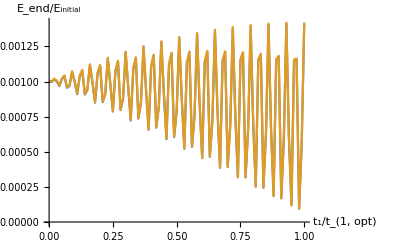

```mathematica
configlist1=Table[{j,(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T1-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)[[1]][[1]]/E10},{j,0,T1/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]],0.01}];
configlist2=Table[{j,(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T2-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)[[1]][[1]]/E20},{j,0,T1/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]],0.01}];

ListPlot[{configlist1,configlist2},AxesOrigin->{0,0},AxesLabel->{Style["t_1/t_(1, opt)",18,Bold],Style["E_end/E_initial",16,Bold]},Joined->True]
```

### für beide Systeme in jeweiliger Gesamtzeit

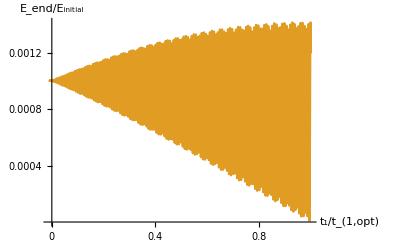

```mathematica
configlist1=Table[{j,((switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T1-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)[[1]][[1]]+(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T1-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)[[1]][[1]])/(E10+E20)},{j,0,T1/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]],0.01}];
configlist2=Table[{j*T1/T2,((switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T2-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)[[1]][[1]]+(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T2-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)[[1]][[1]])/(E10+E20)},{j,-0.01,T2/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]],0.001}];
ListPlot[{configlist1,configlist2},AxesOrigin->{-0,0},AxesLabel->{Style[Row[{Subscript["t",1 ],Style["/",18],Subscript["t",Row[{1,",",Style["opt ",Plain]}]]}],18,Italic],Style[Row[{Subscript["E",Style["end ",Plain]],Style["/",18],Subscript["E",Style["initial",Plain]]}],18,Italic]},Ticks->{{0,0.2,0.4,0.6,0.8,1},{0.0004,0.0008,0.0012}},TicksStyle->{16,16},Joined->True]
```

```mathematica
t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]
```

ArcSec[49/(-81+9 √130)]/(2 √65)

### für beide Systeme mit anderer Gesamtzeit (im Intervall zwischen den beiden optimalen Steuerzeiten für die Enzelsysteme)

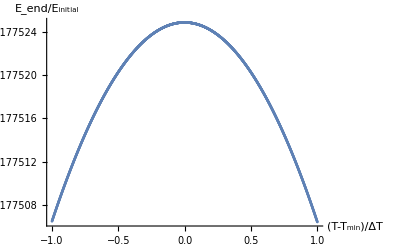

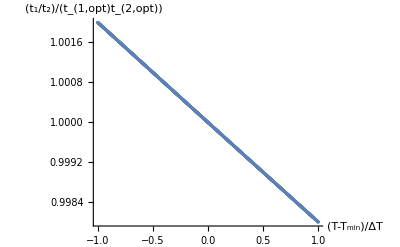

```mathematica
Subscript[ω, 1i]=1000;
Subscript[ω, 2i]=995;
Subscript[ω, f]=1;
x1=0.6;
Temperature=Sqrt[Subscript[ω, 1i]^2+1]/(ArcTanh[-Sqrt[x1]]);
x2=(Tanh[Sqrt[Subscript[ω, 2i]^2+1]/Temperature])^2;
Subscript[ω, min]=1000;
Subscript[ω, max]=1;
E10=Sqrt[x1*(Subscript[ω, 1i]^2+1)];
E20=Sqrt[x2*(Subscript[ω, 2i]^2+1)];
t1[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w1^2+1])*ArcSec[(w2-w1)*(w1-wi)/((1+w1*w2)*(1+w1*wi)-Sqrt[wi^2+1]/Sqrt[wf^2+1]*(1+w1^2)*(1+w2*wf))];
t2[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w2^2+1])*ArcSec[(w1-w2)*(wf-w2)/((1+w2^2)*Sqrt[wf^2+1]/Sqrt[wi^2+1]*(1+w1*wi)-(1+w1*w2)*(1+w2*wf))];
switchmatrix[wi_,wf_]:={{(1+wf*wi)/(1+wi^2),(wi-wf)/(1+wi^2),0},{(wf-wi)/(1+wi^2),(1+wi*wf)/(1+wi^2),0},{0,0,Sqrt[(wf^2+1)/(wi^2+1)]}};
drivingmatrix[t_,w_]:={{1,0,0},{0,Cos[2*Sqrt[w^2+1]*t],-Sin[2*Sqrt[w^2+1]*t]},{0,Sin[2*Sqrt[w^2+1]*t],Cos[2*Sqrt[w^2+1]*t]}};
state1={{E10},{0},{0}};
state2={{E20},{0},{0}};
T1=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]];
T2=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]];
list={};
timelist={};
For[T=Min[{T1,T2}]-Abs[T1-T2],T<Max[{T1,T2}],T=T+Abs[T1-T2]/1000,
configlist=Table[{j,((switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)[[1]][[1]]+(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)[[1]][[1]])/(E10+E20)},{j,0.99,1.01,0.00001}];
energytable=Table[configlist[[k]][[2]],{k,1,Length[configlist]}];
AppendTo[list,{N[(T-Min[{T1,T2}])/(Abs[T1-T2])],Max[energytable]}];
AppendTo[timelist,{N[(T-Min[{T1,T2}])/(Abs[T1-T2])],Sort[configlist,#1⟦2⟧<#2⟦2⟧&]⟦Length[configlist]⟧⟦1⟧/(T/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]-Sort[configlist,#1⟦2⟧<#2⟦2⟧&]⟦Length[configlist]⟧⟦1⟧)/(t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]/t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]])}]
];
ListPlot[list,AxesLabel->{Style[Row[{"(T-",Subscript["T",Style["min",Plain]],")/ΔT"}],18,Italic],Style[Row[{Subscript["E",Style["end",Plain]],"/",Subscript["E",Style["initial",Plain]]}],18,Italic]}]
ListPlot[timelist,AxesLabel->{Style[Row[{"(T-",Subscript["T",Style["min",Plain]],")/ΔT"}],18,Italic],Style[Row[{"(",Subscript["t",1],"/",Subscript["t",2],")/(",Subscript["t",Row[{"1,",Style["opt",Plain]}]],Subscript["t",Row[{"2,",Style["opt",Plain]}]],")"}],18,Italic]}]
```

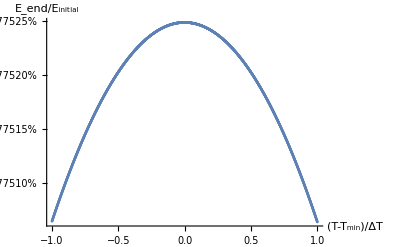

-Graphics-

```mathematica
ListPlot[Table[{list⟦i⟧⟦1⟧,list⟦i⟧⟦2⟧*100},{i,1,Length[list]}],AxesLabel->{Style[Row[{" (T-",Subscript["T",Style["min",Plain]],")/ΔT"}],18,Italic],Style[Row[{Subscript["E",Style["end",Plain]],"/",Subscript["E",Style["initial",Plain]]}],18,Italic]},TicksStyle->{16,16},Ticks->{Automatic,{{0.14177510,"0.14177510%"},{0.14177515,"0.14177515%"},{0.14177520,"0.14177520%"},{0.14177525,"0.14177525%"}}}]
ListPlot[timelist,AxesLabel->{Style[Row[{" (T-",Subscript["T",Style["min",Plain]],")/ΔT"}],18,Italic],Style[Row[{"(",Subscript["t",1],"/",Subscript["t",2],")/(",Subscript["t",Row[{"1,",Style["opt",Plain]}]],Subscript["t",Row[{"2,",Style["opt",Plain]}]],")"}],18,Italic]},TicksStyle->{16,16}]
```

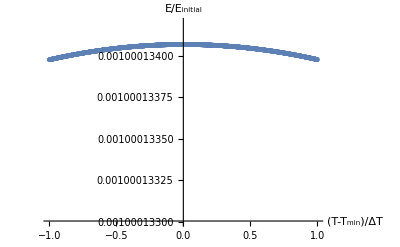

```mathematica
ListPlot[list,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["E/E_initial",14,Bold,Italic]},PlotRange->{{-1,1},{0.001000133,0.0009991}}]
```

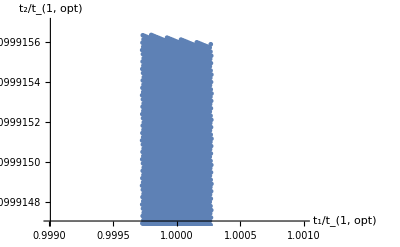

```mathematica
ListPlot[timelist,AxesLabel->{Style["t_1/t_(1, opt)",14,Bold,Italic],Style["t_2/t_(1, opt)",14,Bold,Italic]},PlotRange->{{0.999,1.001},{0.000999147,0.000999157}}]
```

```mathematica
newlist=Table[{-1+j/1000,(timelist[[j+1]][[1]]/timelist[[j+1]][[2]])/(t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]/t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]])},{j,0,1999}];
```

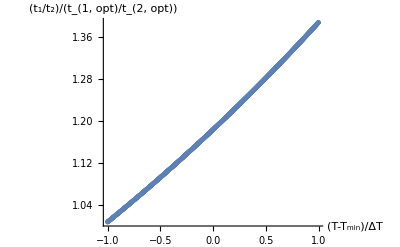

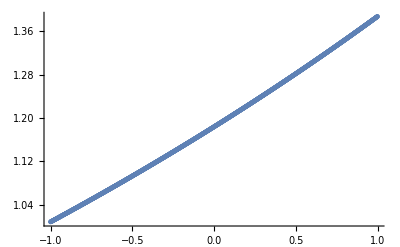

```mathematica
ListPlot[newlist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["(t_1/t_2)/(t_(1, opt)/t_(2, opt))",14,Bold,Italic]}]
```

```mathematica
newlist[[1]]
```

{-1,(1.0083 ArcSec[49/(-81+(65 √2 (1+ω_0))/(√(1+ω_0^2)))])/ArcSec[(7 (1-ω_0))/(9 (1+ω_0)-9 √2 √(1+ω_0^2))]}

```mathematica
Length[timelist]
```

2000

```mathematica
sortedlist=Sort[list,#1[[2]]<#2[[2]]&];
```

```mathematica
sortedlist[[Length[list]]]
```

{0.287,0.214448}

```mathematica
sortedlist[[1]][[2]]/sortedlist[[Length[list]]][[2]]
```

0.999997

```mathematica
timelist[[1000+287]]
```

{1.06201,0.150345}

### für beide Systeme mit anderer Gesamtzeit (größere als die längste optimale Steuerzeit der Einzelsysteme)

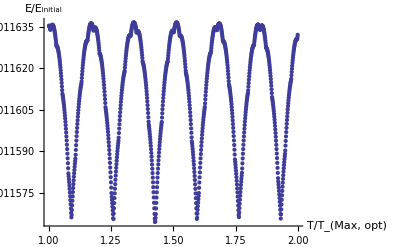

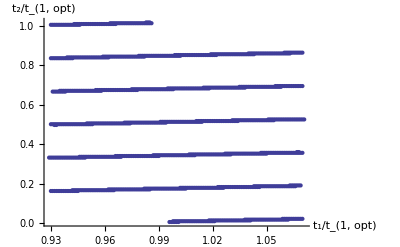

```mathematica
T1=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]];
T2=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]];
list={};
timelist={};
For[T=Max[{T1,T2}],T<2*Max[{T1,T2}],T=T+Max[T1,T2]/1000,
configlist=Table[{j,((switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)[[1]][[1]]+(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)[[1]][[1]])/(E10+E20)},{j,0,T/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]],0.001}];
energytable=Table[configlist[[k]][[2]],{k,1,Length[configlist]}];
AppendTo[list,{N[T/(Max[T1,T2])],Max[energytable]}];
AppendTo[timelist,{Sort[configlist,#1⟦2⟧<#2⟦2⟧&]⟦Length[configlist]⟧⟦1⟧,T/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]-Sort[configlist,#1⟦2⟧<#2⟦2⟧&]⟦Length[configlist]⟧⟦1⟧}]
];
ListPlot[list,AxesLabel->{Style["T/T_(Max, opt)",14,Bold,Italic],Style["E/E_initial",14,Bold,Italic]}]
ListPlot[timelist,AxesLabel->{Style["t_1/t_(1, opt)",14,Bold,Italic],Style["t_2/t_(1, opt)",14,Bold,Italic]}]
```

```mathematica
sortedlist=Sort[list,#1[[2]]<#2[[2]]&];
```

```mathematica
sortedlist[[1]]
```

{1.33,0.206134}

```mathematica
Length[timelist]
```

100

```mathematica
timelist[[33]]
```

{1.6,0.12205}

### alle Punkte grob gerastert

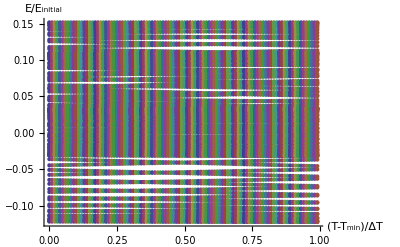

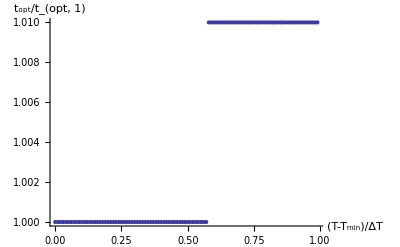

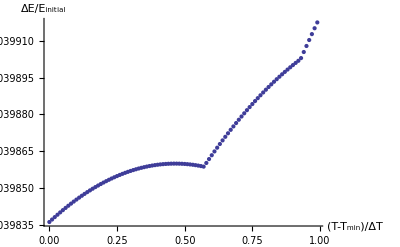

```mathematica
T1=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]];
T2=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]];
energylist={};
optimaltimelist={};
spreadlist={};
incrementt1=0.01;
incrementT=0.01;
For[T=Min[{T1,T2}],T<Max[{T1,T2}],T=T+Abs[T1-T2]*incrementT,
configlist=Table[{j,((switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)⟦1⟧⟦1⟧+(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)⟦1⟧⟦1⟧)/(E10+E20)},{j,0,T/t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]],incrementt1}];
energytable=Table[{(T-Min[{T1,T2}])/(Abs[T1-T2]),configlist⟦k⟧⟦2⟧},{k,1,Length[configlist]}];
AppendTo[energylist,energytable];
AppendTo[optimaltimelist,{(Abs[T-T2])/Abs[T1-T2],(Flatten[Position[Table[configlist[[k]][[2]],{k,1,Length[configlist]}],Max[Table[configlist[[k]][[2]],{k,1,Length[configlist]}]]]]⟦1⟧-1)*incrementt1}];
AppendTo[spreadlist,{(Abs[T-T2])/Abs[T1-T2],(Max[Table[configlist[[k]][[2]],{k,1,Length[configlist]}]]-Min[Table[configlist[[k]][[2]],{k,1,Length[configlist]}]])/(E10+E20)}];
]
ListPlot[energylist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["E/E_initial",14,Bold,Italic]}]
ListPlot[optimaltimelist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["t_opt/t_(opt, 1)",14,Bold,Italic]}]
ListPlot[spreadlist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["ΔE/E_initial",14,Bold,Italic]}]
```

### alle Punkte fein gerastert

-Graphics-

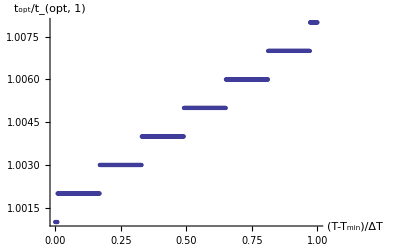

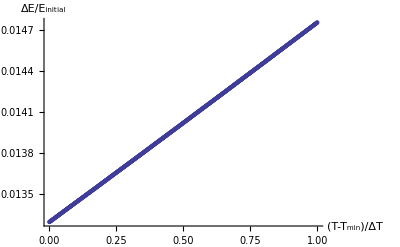

```mathematica
T1=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]];
T2=t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]]+t2[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 2i],Subscript[ω, f]];
energylist={};
optimaltimelist={};
spreadlist={};
incrementt1=0.001;
incrementT=0.001;
startfractiont1=0.9;
endfractiont1=1.1;
For[T=Min[{T1,T2}],T<Max[{T1,T2}],T=T+Abs[T1-T2]*incrementT,
configlist=Table[{j,((switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 1i],Subscript[ω, max]].state1)⟦1⟧⟦1⟧+(switchmatrix[Subscript[ω, min],Subscript[ω, f]].drivingmatrix[T-t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, min]].switchmatrix[Subscript[ω, max],Subscript[ω, min]].drivingmatrix[t1[Subscript[ω, max],Subscript[ω, min],Subscript[ω, 1i],Subscript[ω, f]]*j,Subscript[ω, max]].switchmatrix[Subscript[ω, 2i],Subscript[ω, max]].state2)⟦1⟧⟦1⟧)/(E10+E20)},{j,startfractiont1,endfractiont1,incrementt1}];
energytable=Table[{(T-Min[{T1,T2}])/(Abs[T1-T2]),configlist⟦k⟧⟦2⟧},{k,1,Length[configlist]}];
AppendTo[energylist,energytable];
AppendTo[optimaltimelist,{(T-Min[T1,T2])/Abs[T1-T2],(Flatten[Position[Table[configlist[[k]][[2]],{k,1,Length[configlist]}],Max[Table[configlist[[k]][[2]],{k,1,Length[configlist]}]]]]⟦1⟧-1)*incrementt1+startfractiont1}];
AppendTo[spreadlist,{(T-Min[{T1,T2}])/Abs[T1-T2],(Max[Table[configlist[[k]][[2]],{k,1,Length[configlist]}]]-Min[Table[configlist[[k]][[2]],{k,1,Length[configlist]}]])/(E10+E20)}];
]
ListPlot[energylist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["E/E_initial",14,Bold,Italic]}]
ListPlot[optimaltimelist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["t_opt/t_(opt, 1)",14,Bold,Italic]}]
ListPlot[spreadlist,AxesLabel->{Style["(T-T_min)/ΔT",14,Bold,Italic],Style["ΔE/E_initial",14,Bold,Italic]}]
```